```mathematica
data=FinancialData["HK:01810","OHLCV",{{2020,9,1},Now}]
```

{{{2020,9,1},{23.8,25.6,23.55,25.6,385280000}},{{2020,9,2},{26.6,26.95,24.7,25.7,442670000}},{{2020,9,3},{25.45,25.75,23.55,23.9,399250000}},{{2020,9,4},{22.15,24.95,22.,24.5,758760000}},{{2020,9,7},{24.3,25.,23.65,24.15,443060000}},{{2020,9,8},{24.5,24.7,21.8,22.4,348240000}},{{2020,9,9},{21.8,22.65,20.95,22.1,253200000}},{{2020,9,10},{22.5,23.3,22.3,22.45,160520000}},{{2020,9,11},{22.65,23.35,22.3,23.25,162210000}},{{2020,9,14},{23.45,23.95,22.85,23.55,130450000}},{{2020,9,15},{22.5,22.85,22.1,22.35,644590000}},{{2020,9,16},{22.45,22.85,22.25,22.75,134730000}},{{2020,9,17},{22.55,22.65,21.2,21.3,231540000}},{{2020,9,18},{21.45,22.15,21.4,22.05,156720000}},{{2020,9,21},{22.2,22.3,20.6,20.6,187320000}},{{2020,9,22},{20.65,21.25,20.3,20.45,129290000}},{{2020,9,23},{20.65,21.1,20.45,20.85,101050000}},{{2020,9,24},{20.55,20.55,19.8,19.84,170830000}},{{2020,9,25},{20.15,20.3,19.4,19.72,136210000}}}

```mathematica
data1={#[[1]],#[[2,1]]}&/@data
```

{{{2020,9,1},23.8},{{2020,9,2},26.6},{{2020,9,3},25.45},{{2020,9,4},22.15},{{2020,9,7},24.3},{{2020,9,8},24.5},{{2020,9,9},21.8},{{2020,9,10},22.5},{{2020,9,11},22.65},{{2020,9,14},23.45},{{2020,9,15},22.5},{{2020,9,16},22.45},{{2020,9,17},22.55},{{2020,9,18},21.45},{{2020,9,21},22.2},{{2020,9,22},20.65},{{2020,9,23},20.65},{{2020,9,24},20.55},{{2020,9,25},20.15}}

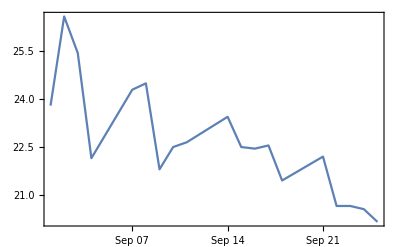

```mathematica
DateListPlot@data1
```